Exercisi 0: Copiar el programa de les funcions predefinides de la bisseccio:

```mathematica
Biseccio[f_,{a_,b_,M_}]:=Module[{an,bn,xn},
an=a;
bn=b;
For[i=1,i≤M,i++,
xn=N[(an+bn)/2,20];
If[f[xn]==0,Break[],
If[f[an]*f[xn]<0, bn=xn,
If[f[xn]*f[bn]<0,an=xn]
]
]
];
N[xn,20]
]
```

Exercisi 1

```mathematica
N[Log[10^11] / Log[2]]
```

36.5412

```mathematica
f[x_] = x^3 - 5
```

-5+x^3

```mathematica
Biseccio[f,{1,2,37}]
```

1.7099759466727846302

Exercisi 2

```mathematica
F[x_]=x^2-Cos[x]+Sin[x]
```

x^2-Cos[x]+Sin[x]

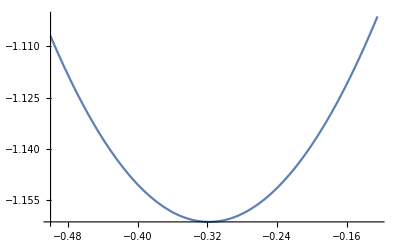

```mathematica
Plot [F[x],{x,-0.5,-0.125}]
```

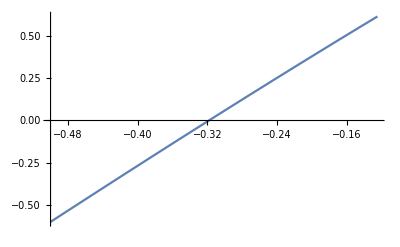

```mathematica
Plot [F'[x],{x,-0.5,-0.125}]
```

```mathematica
N[Log[10^11*0.375] / Log[2]]
```

35.1262

```mathematica
Biseccio[F',{-0.5,-0.125,36}]
```

-0.318366

Exercisi 3.1 Definir metode de Newton. Despres està l’activitat

```mathematica
Newton[f_,x0_,M_]:=Module[{xn},
xn=x0;
For[i=1, i≤M, i++,
xn=xn-f[xn]/f'[xn]
];
N[xn,20]
]
```

```mathematica
f[x_]=3x-x^3+4
```

4+3 x-x^3

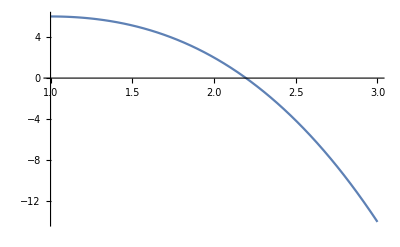

```mathematica
Plot[f[x],{x,1,3}]
```

```mathematica
Newton[f,2,4]
```

2.1958233454456516143

```mathematica
NSolve[f[x]==0,x,WorkingPrecision->20]
```

{{x→-1.0979116727228235764-0.7850032632435902184 ⅈ},{x→-1.0979116727228235764+0.7850032632435902184 ⅈ},{x→2.1958233454456471528}}

Han eixit uns 14 decimals exactes de la Newton amb 4 iteracions al NSolve.

Exercisi 4. Anar augmentant el nombre d’iteracions fins que done el resultat de la activitat 2, que era -0.318366. Amb 3 iteracions es suficient amb el metode Newton. Mentre que en la act 2 feien falta 36

```mathematica
Newton[F',-0.5,1]
```

-0.32072

```mathematica
Newton[F',-0.5,2]
```

-0.318367

```mathematica
Newton[F',-0.5,3]
```

-0.318366